# 基础

## 圆周率小数点后1,024位热图

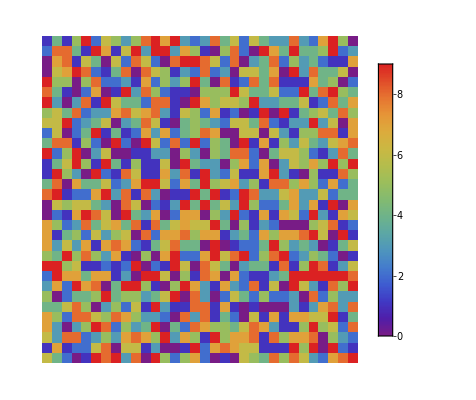

```mathematica
pi=N[Pi,1024+1];
piString=StringDelete[ToString[pi],"3."];(*将 pi 转换为字符串，并删除小数点*)
piList=ToExpression/@Characters[piString];(*将 piString 转换为数字列表*)
piArray=Partition[piList,32]; (*将 piList 按照每行 32 个数字的方式重新排列*)
ArrayPlot[piArray,ColorFunction->"Rainbow",PlotTheme->"Detailed"]
```

## 圆周率小数点后数字统计

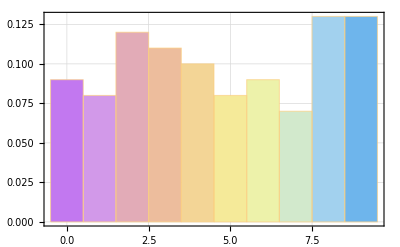
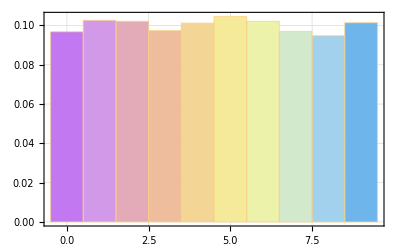
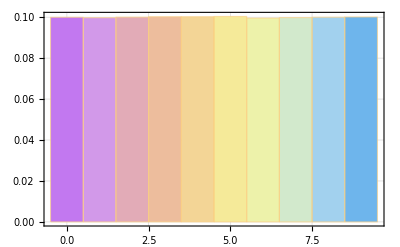

```mathematica
Histogram[RealDigits[N[Pi,#+1]-3][[1]](*圆周率小数点后的数字放在数组里*),{1},"PDF",PlotTheme->"Detailed",ChartStyle->"Pastel"]&/@{100,10000,1000000}(*小数点后位数*)
```

## 随正多边形边数不断增大时圆周率的估算情况

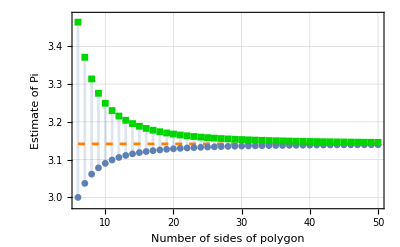

```mathematica
Show[DiscretePlot[{n Sin[Pi/n],n Tan[Pi/n]},{n,6,50},PlotRange->{{6,50},{2.98,3.48}},Filling->{1->{2}},PlotStyle->{Default,Darker[Green,1/6]},Frame->True,GridLines->Automatic,PlotMarkers->{Automatic, Small},FrameLabel->{"Number of sides of polygon","Estimate of Pi"}],Plot[Pi,{x,6,96},PlotStyle->{Orange,Dashed}]]
```

## 阿基米德估算圆周率

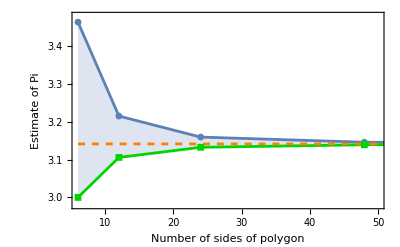

```mathematica
{an,bn}=NestList[{2 #[[1]] #[[2]]/(#[[1]]+#[[2]]),Sqrt[(2 #[[1]] #[[2]]/(#[[1]]+#[[2]])) #[[2]]]}&,{6 Tan[Pi/6],6 Sin[Pi/6]},4]//N//Transpose;

xn=Table[6 2^n,{n,0,4}];

Show[ListLinePlot[Transpose@{xn,#}&/@{an,bn},PlotMarkers->{Automatic, Small},PlotRange->{{6,50},{2.98,3.48}},Filling->{1->{2}},PlotStyle->{Default,Darker[Green,1/6]},Frame->True,FrameLabel->{"Number of sides of polygon","Estimate of Pi"}],Plot[Pi,{x,6,96},PlotStyle->{Orange,Dashed}]]
```

## 二项式展开单项系数

```mathematica
StemPlot[n_]:=DiscretePlot[Binomial[n,k],{k,0,n},PlotRange->All,PlotMarkers->{Automatic,Small},AxesLabel->{"Degree","Coefficient"},PlotLabel->"Binomial Coefficients"]
```

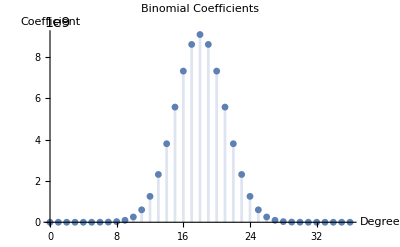

```mathematica
StemPlot[36]
```